# Mathematical Analysis Exam 3

## May 1, 2025. As always, and actually, on any exam from any professor, if you get bogged down on a problem, move on and come back later.

## Chapter 9 — Derivatives

Here is the definition of the derivative, which I didn’t ask you to memorize, but I hope you have:
-Graphics-

### 1. Application of the Definition of the Derivative

-Graphics-

In your proof, you may use any property of limits that we obtained prior to Chapter 9. The point is not to reprove things we already proved. The point is to apply the arsenal of facts developed in Chapters 1-8 to make a new result easy.

## Chapter 10 — Differentiation

### 2. Application of Differentiation Rules

Find f'(x) for each of the two following functions f. Don’t worry about the domain of f or f' if they have some points where they are ill-defined. The goal here is not proofs. The goal is to accurately apply sum rule, product rule, quotient rule, and chain rule.

-Graphics-

### 3. Obtain a Fancy Quotient Rule

Let A, B, C, D be four functions. Let f=(A·B)/(C·D).

NB: Those are times signs not composition of function symbols between A and B and between C and D.

By application of the quotient rule, and by two applications of the product rule, get a pleasingly symmetrical expression for f'. By pleasingly symmetrical, there should be four terms over a common denominator, and it should be clear that the exchanges, A<->B and C<->D, which clearly do not affect f, also do not affect f'.

## Chapter 11 — The Significance of the Derivative

## On the next page is a piece of graph paper. Separate it from the exam to use for the next problem.

### 4. Using Derivatives to Aid Graphing

Consider the function f(x)=x+4/x.

(a) By taking a derivative, setting it equal to zero, and solving, you will find two values of x where f'(x)=0.

(b) Now that you have found those two values of x, what are the two values of f(x), at those points?

(c) 4/x becomes negligible when x is huge and positive or huge and negative. If we could neglect  4/x completely, we would just have the function f(x)=x. Of course we can’t neglect  4/x completely. Use a ruler to draw the function f(x)=x with dashed lines on a piece of graph paper. The lines going off to plus and minus infinity you have drawn are called “asymptotes.”

(d) Add the two points you found in (a) and (b) to the graph. Lightly draw a horizontal line through each of those two points to indicate that the tangent to f(x) has slope 0 at those points.

(e) Using what you learned in (a)-(d) quickly and crudely sketch the full function  f(x)=x+4/x with solid lines. Your solid lines will approach but never touch the asymptotes as x->∞ or x->-∞.

## Graph Paper for Problem 4.

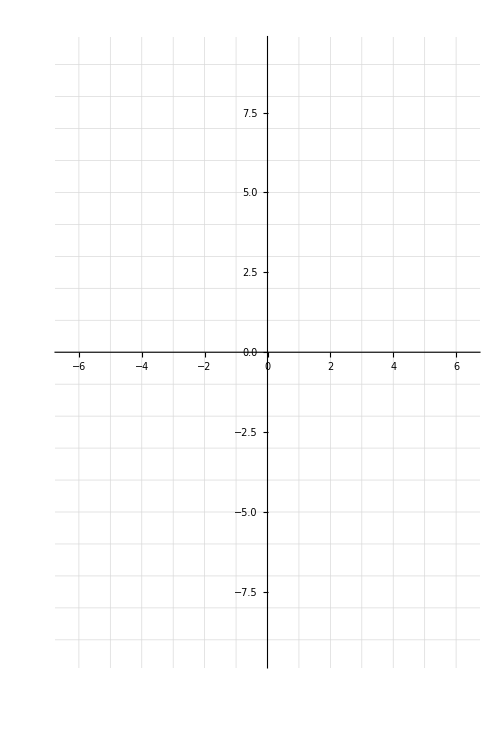

```mathematica
Plot[{},{x,-6.5,6.5},PlotRange->{{-6.5,6.5},{-9.5,9.5}},AspectRatio->9.5/6.5,Frame->False,GridLines->{Range[-6,6,1], Range[-9,9,1]},GridLinesStyle->Medium,AxesStyle->Thick]
```

### 5. A Simple Optimization Problem

The trajectory of a particle undergoing parabolic motion with no friction is:

Horizontal motion:

x(t)=v_0 t cosθ

Vertical motion:

y(t)=v_0 t sinθ-1/2 g t^2

In these equations v_0 and g are positive constants (the muzzle velocity and the acceleration of gravity). The time t is the variable. For the moment θ is just another constant.

(a) Take y'(t), set it to 0, and use this to find the time of maximum height.

(b) Double the time you found in (a). Because it takes as long to reach maximum height as to come back to the ground, by doubling the time, you have found the time of impact. Now put the time of impact into the formula for the horizontal motion.

(c) You found the formula for the distance to impact in (b). This is called the “range.” Your formula no longer involves time. Now think of θ as the variable and take the derivative of the range R(θ) with respect to θ, and set that to 0. That will tell you what angle θ gives the maximum range. If you know even a little trig, you will see what angle this is: -Graphics-

## Chapter 12 — Inverse Functions

Here is our favorite theorem (Theorem 5) from the inverse functions chapter:

-Graphics-

### 6. Leibniz Notation for Theorem 5

(a) Do what Spivak asks in Problem 17 of Chapter 12, which is simply to rewrite

             f^(-1 ')=1/f'
             
    in Leibniz notation. Here is the way Spivak asked it:

-Graphics-

Leave the letters a and b out of your rewrite. You can do this because it is understood in Leibniz notation that dy/dx is evaluated at x and dx/dy is evaluated at y, and that x=f^-1(y).

NOTE: What you got is the sort of thing that people that like Leibniz notation do as if it were dx and dy were “infinitesimal” numbers which can be divided like ordinary numbers.

(b) For the inverse functions y=x^(1/n) and x=y^n, what is dx/dy? I am just asking you to differentiate x=y^n with respect to y.

(c) Since the inverse function is y=x^(1/n), we can write dy/dx=(d x^(1/n))/dx. Use that to rewrite what you got in (a). Also use what you got in (b) in the denominator of what you got in (a).

NO CREDIT, JUST A CHECK ON YOUR WORK: If you want to check that you got something sensible in (c), you can now put back in that y=x^(1/n) in the denominator. If you simplify, you will get something you already knew to be true.

## Chapter 13 — Integrals

### 7. A Standard Integral

If you do the integral of x^2 from 0 to b, the answer is b^3/3. Let’s do a few steps of the proof of that following along with what Spivak did for the function x from 0 to b on pp. 258-9. In the interest of time, I am going to do the first few steps for you:

If you partition the region from 0 to b into n equal parts, each has width b/n and the lower sum is:

L(f,n)=∑_(i=0)^(n-1) (ib/n)^2 b/n=∑_(i=1)^(n-1) (ib/n)^2 b/n.

(I used that the i=0 term contributes nothing.)

Meanwhile, the upper sum is:

U(f,n)=∑_(i=1)^n (ib/n)^2 b/n.

(a) What is a pleasantly simple expression for the difference:

U(f,n)-L(f,n)=∑_(i=1)^n (ib/n)^2 b/n-∑_(i=1)^(n-1) (ib/n)^2 b/n

(b) The upper sum always approaches the value of the integral from above, and the lower sum always approaches it from below. We want to “squeeze” in on the value of the integral from either side to show that the integral exists. To make the difference you found in (a) less than ϵ, how must we choose n as a function of b and ϵ?

## Chapter 14 — The Fundamental Theorem of Calculus

### 8. Two Applications of the (The First) Fundamental Theorem of Calculus

(a) Find a function g(x) that satisfies:

∫_0^x tg(t)dt=x+x^2

(b) Repeat, but for the slightly trickier problem:

∫_0^(x^2) tg(t)dt=x+x^2

## NAME: _____________________________

## 1 /3 2 /3 3 /3 4 /4 5 /4 6 /3 7 /2 8 /3 ============= TOTAL / 25